```mathematica
Clear["Global`*"]
```

```mathematica
adag[Ν_]:=Table[KroneckerDelta[m,n+1] √(n+1),{m,0,Ν-1},{n,0,Ν-1}]
a[Ν_]:=Table[KroneckerDelta[m,n-1] √n,{m,0,Ν-1},{n,0,Ν-1}]
```

```mathematica
h[λ_,β_,Ν_]:=-λ/4 MatrixPower[adag[Ν]-a[Ν],2]+1/(4 λ) MatrixPower[adag[Ν]+a[Ν],2]+β/λ^2 MatrixPower[adag[Ν]+a[Ν],4]
```

```mathematica
diagonalize[λ_,β_,Ν_]:=Eigensystem[N[h[λ,β,Ν]]]
```

```mathematica
ψ[n_,x_,λ_]:=1/(√(2^n n!)) (λ/(2 π))^(1/4) Exp[-(λ x^2)/4] HermiteH[n,√(λ/2) x]
```

```mathematica
plotEigenfct[λ_,n_,diagH_]:=Module[{wavefct=Sum[diagH[[2,-n-1,m]] ψ[m-1,x,λ],{m,1,Length[diagH[[2]]]}]},
Plot[Abs[wavefct]^2,{x,-3,3},PlotLabel->diagH[[1,-n-1]],PlotRange->{0,.7}]
]
```

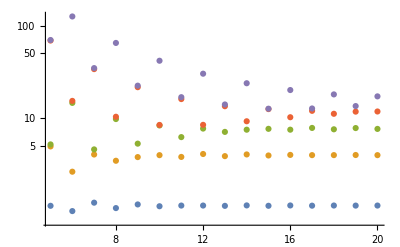

```mathematica
ListLogPlot[Table[{#,diagonalize[1,1,#][[1,#-j]]}&/@Table[i,{i,5,20}],{j,0,4}],PlotRange->All]
```

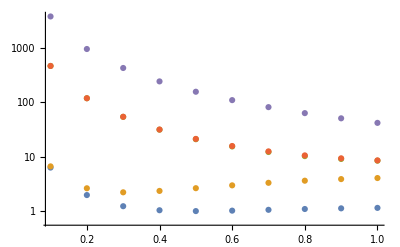

```mathematica
ListLogPlot[Table[{#,diagonalize[#,1,10][[1,10-j]]}&/@Table[i,{i,.1,1,.1}],{j,0,4}],PlotRange->All]
```

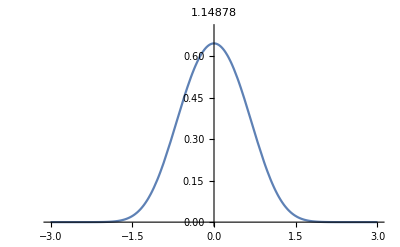
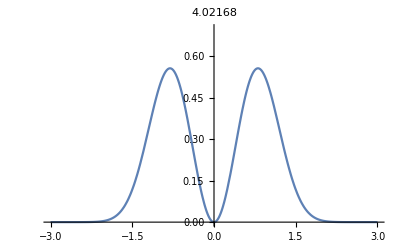
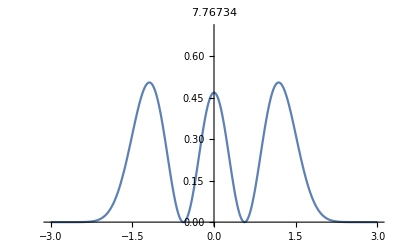
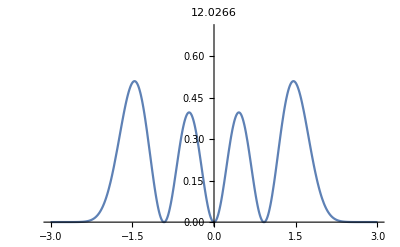
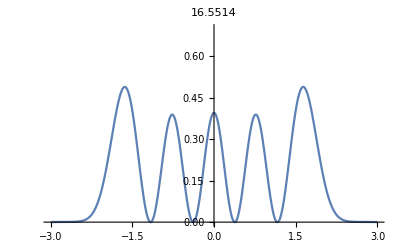

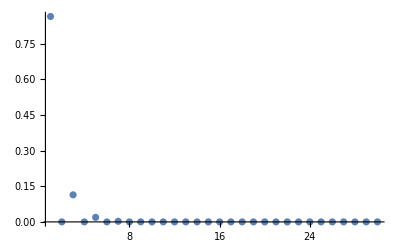
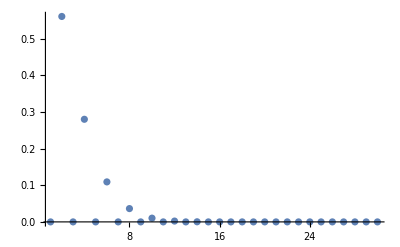
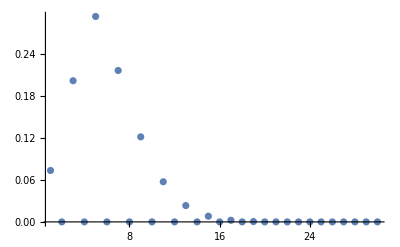

```mathematica
d1=diagonalize[1,1,30];
Table[plotEigenfct[1,i,d1],{i,0,4}]
Table[ListPlot[Abs[d1[[2,-i-1]]]^2,PlotRange->All],{i,0,4}]
```

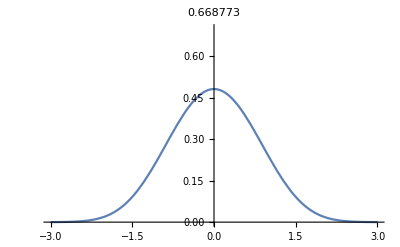
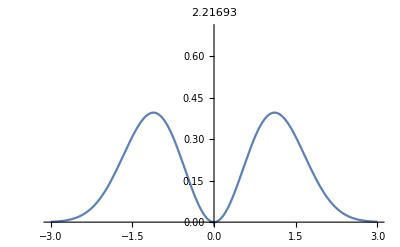
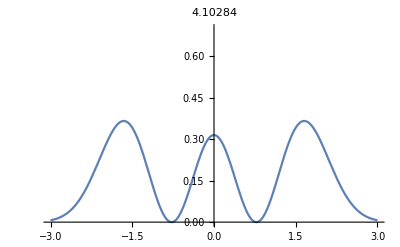
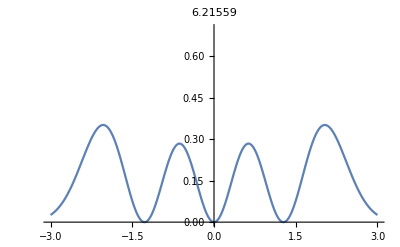
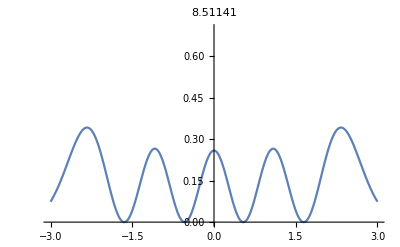

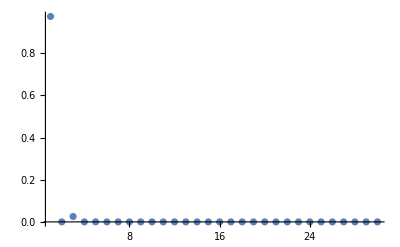
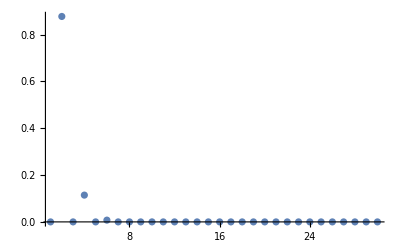
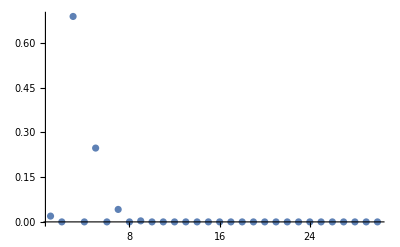

```mathematica
d2=diagonalize[1,10^-1,30];
Table[plotEigenfct[1,i,d2],{i,0,4}]
Table[ListPlot[Abs[d2[[2,-i-1]]]^2,PlotRange->All],{i,0,4}]
```

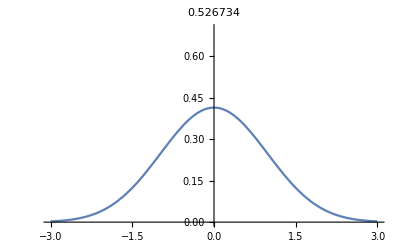
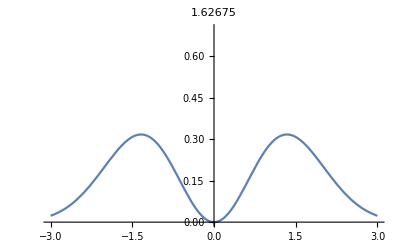
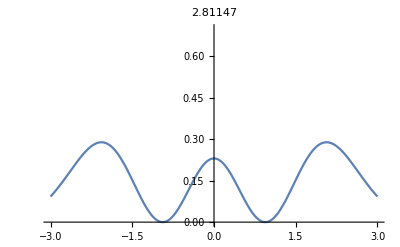
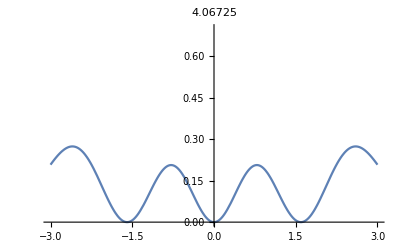
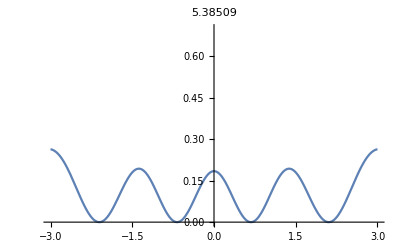

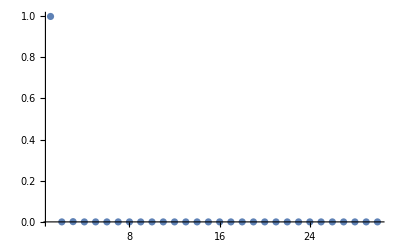
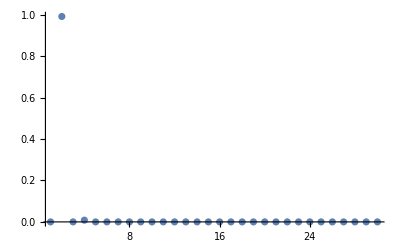
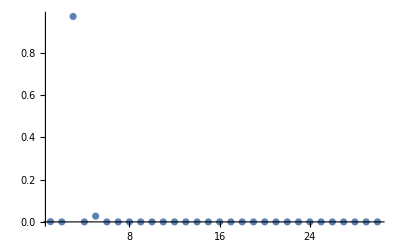

```mathematica
d3=diagonalize[1,10^-2,30];
Table[plotEigenfct[1,i,d3],{i,0,4}]
Table[ListPlot[Abs[d3[[2,-i-1]]]^2,PlotRange->All],{i,0,4}]
```